# Precipitation Predictability over Extended Lead Time for West Coast United States

BX Pan
2017.10.22

## Background

The Quiet Revolution of Numerical Weather Prediction

```mathematica
ECMWF=Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/RevolutionOfECMWF.png"],
		1000],
	"Fig1. Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015",Bottom]
```

-Graphics-Fig1. Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015

```mathematica
NCEP=Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/RevolutionOfNCEP.png"],
		1000],
	"Fig2. Predictability(Mean Error) of North America 500hpa GPH from NCEP,  NCEP Central Operations, March, 2016",Bottom]
```

-Graphics-Fig2. Predictability(Mean Error) of North America 500hpa GPH from NCEP,  NCEP Central Operations, March, 2016

Could “S2S forecasts be as widely used a decade from now as weather forecasts are today”?

Stretch the lead time of weather timescale models forward and climate models backward.

The Ongoing Inquiry of the Foundation of “Climate Projection”

```mathematica
TableForm[{{"Initial Value Problem","Deterministic"},
           {"Boundary Value Problem","Proabilisitc"}},
          TableHeadings->{{"Weather Forecast","Climate Prediction"},None}]
```

Weather Forecast | Initial Value Problem | Deterministic
Climate Prediction | Boundary Value Problem | Proabilisitc

A deterministic system could be unpredictable:

Is the earth’s weather system ergodic? (more illustrations should be added here)

If it was ergodic, will an imperfect model be a valid predictor for the climate’s statistical features?

The Emerging Demand for Accurate and Extended Quantitative Precipitation Forecast(QPF)

```mathematica
Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/DemandForS2S.png"],1000],
	 "Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.",Bottom]
```

-Graphics-Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.

Predictability for extratropical and tropical areas are different, due to different precipitation mechanisms.

```mathematica
ImageResize[xkcdConvert[ListLinePlot[{{{1,0.86},{2,0.85},{3,0.75},{4,0.7},{5,0.65},{7,0.5},{10,0.3},{12,0.13},{14,0.13},{20,0.135},{30,0.2}},
              {{1,0.7},{2,0.65},{4,0.5},{7,0.45},{14,0.4},{20,0.42},{30,0.43}}},
              PlotStyle->{Blue,Red},
              Frame->True,
              Ticks->None,
              FrameLabel->{"Forecast Leading Days","Predictability"},
              Epilog -> 
   xkcdLabel /@ {{"Extratropic", {3, 0.75}, {1, 0}}, {"Tropic", {4, 0.5}, {0, -0.3}}}]],700]
```

-Graphics-

Extratropical predictability is mostly derived from synoptic-scale atmospheric dynamics

Tropical predictability is primarily derived from the response of moist convection to
slowly varying forcing such as from ENSO.

Subseasonal to Seasonal Prediction Project (2013-2018)

## Opportunities and Challenges

sampling effect?

California

38 million people(12% total US population)
9 million irrigated acres farm that lead the nation in production
demand for hydroelectricity from the state’s 13765 MW of capacity

#### California Department of Water Resources’s forecast of total April-July river runoff. water-year based indices

USDA Natural Resources Conservation Service in partnership with NOAA/National Weather Service

Snowpack

Oregon

Washington

Capacity to Predict MJO (average gain of 1 day of prediction skill per year)

Teleconnection between MJO and extratropics

North Atlantic Oscillation Index

2m temperature anormalies

Tropical Cyclones

Extratropical Storm Tracks

## Research Question

Where we are now in the respect of S2S predictability?

Dynamical Methods

Statistical Methods

## Literature Review

The most important aspect of the challenge is the chaotic nature of weather and climate predictability that needs to be characterized with probabilistic information.

## Data

S2S, sub-seasonal to seasonal prediction project, is a WWRP/THORPEX-WCRP joint research project established to improve forecast skill and understanding on the sub-seasonal to seasonal time scale, and promote its uptake by operational centres and exploitation by the applications community.

```mathematica
TableForm[{{"","Ocean Model","Sea Ice Model","Landsurface Model",""},
           {"BoM","ACOM2 (Schiller and Godfrey 2003)","",""},
           {"BoM","ACOM2 (Schiller and Godfrey 2003)","",""}}]
```

Initial conditions and perturbations

Data assimilation method for control analysis: Nudging from 4dVar reanalysis
Resolution of model used to generate Control Analysis: T47
Ensemble initial perturbation strategy: Coupled bred vectors
Horizontal and vertical resolution of perturbations:  T47
Perturbations in +/- pairs: no

```mathematica
datasets=Block[{model,primary,size,frequency},
	SetDirectory["/Users/lambda/Documents/Research/3_S2SEvaluation/Data"];
	models=Select[FileNames[],StringFreeQ[#,"."]&];
	primary={
		{Green,"BoM",LinguisticAssistant},    
		{Red,"CMA",LinguisticAssistant},  
		{Purple,"StyleBox[\"ECCC\",FontWeight->\"Bold\"]",LinguisticAssistant}, 
		{Gray,"StyleBox[\"ECMWF\",FontWeight->\"Bold\"]",LinguisticAssistant},
		{Magenta,"StyleBox[\"HMCR\",FontWeight->\"Bold\"]",LinguisticAssistant},   
		{Yellow, "ISAC-CNR",LinguisticAssistant}, 
		{LightPurple,"JMA", LinguisticAssistant},
		{Brown, "StyleBox[\"KMA\",FontWeight->\"Bold\"]",LinguisticAssistant},  
		{Cyan,"Météo-France",LinguisticAssistant},  
		{Blue,"NCEP",LinguisticAssistant},
		{Orange, "StyleBox[\"UKMO\",FontWeight->\"Bold\"]",LinguisticAssistant}};
	size=Map[Block[{data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>".mx"]},
		Dimensions[data[[1]]]][[{1,3}]]&,models];
	frequency=Block[{time,f,e},
		time=Map[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>"_control_time.mx"]&,models];
		f=Map[Round[#[[1]],0.1]&,Map[(DateDifference[#[[1]],#[[-1]]])/(Length[#]+0.0)&,time]];
		e=Map[{#[[1,1]],#[[-1,1]]}&,time];
		Map[If[#[[1]]<1.01,
		"Every day from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]],
		"Every "<>ToString[#[[1]]]<>" days from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]]]&,Transpose[{f,e}]]];
	Map[Flatten,Transpose[{primary,size,frequency}]]];
label=TableForm[Map[Flatten[{#[[1]],#[[2]]<>"("<>ToString[#[[3]][[2]]]<>")",#[[4;;]]}]&,datasets],
	TableHeadings->{None,{"","Model","Ensemble Size","Extension(day)","Hincast Frequency"}},
	TableAlignments->Left];
Labeled[Show[GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets]],
	  GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets[[{6,9,11}]]]],ImageSize->1160],
	  label,Bottom]
(*Export["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/fig1_dataset.pdf",%];*)
```

-Graphics- | Model | Ensemble Size | Extension(day) | Hincast Frequency
RGBColor[0, 1, 0] | BoM(Australia) | 33 | 62 | Every 5.1 days from 1981 to 2013
RGBColor[1, 0, 0] | CMA(China) | 4 | 60 | Every day from 1994 to 2014
RGBColor[0.5, 0, 0.5] | ECCC(Canada) | 4 | 32 | Every 4.1 days from 1995 to 2014
GrayLevel[0.5] | ECMWF(Europe) | 11 | 46 | Every 2.6 days from 1995 to 2016
RGBColor[1, 0, 1] | HMCR(Russia) | 10 | 61 | Every 2.9 days from 1985 to 2010
RGBColor[1, 1, 0] | ISAC-CNR(Italy) | 1 | 31 | Every 5. days from 1981 to 2010
RGBColor[0.94, 0.88, 0.94] | JMA(Japan) | 5 | 34 | Every 10.1 days from 1981 to 2010
RGBColor[0.6, 0.4, 0.2] | KMA(SouthKorea) | 3 | 60 | Every 10.9 days from 1991 to 2010
RGBColor[0, 1, 1] | Météo-France(France) | 15 | 61 | Every 15.2 days from 1993 to 2014
RGBColor[0, 0, 1] | NCEP(UnitedStates) | 4 | 44 | Every day from 1999 to 2010
RGBColor[1, 0.5, 0] | UKMO(UnitedKingdom) | 3 | 60 | Every 7.6 days from 1993 to 2015

## Skill Metric

Consider the synoptic-scale atmospheric dynamics.

For a fair comparison across a seamless range of time scales, the verification is performed using data averaged over time windows equal in length to the forecast lead time

```mathematica
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
models=Select[FileNames[],StringFreeQ[#,"."]&];
RMSE[simu_,obser_]:=Sqrt[Mean[(simu-obser)^2]]
SCA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#≤38.0&)]]]&,models];
NCA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>38.0,#<=42]&)]]]&,models];
OR=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>42.0,#≤45]&)]]]&,models];
WA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#>45&)]]]&,models];
```

```mathematica
Evaluation[dataset_,type_,season_:0,interval_:{1,1},grids_:{1},skill_:Correlation]:=Block[{grid,simu,obser,msimu},
	(*type: grid&daily,grid&interval,regional&daily,regional&interval*)
	grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_grids.mx"];
	{simu,obser}=Block[{osimu,oobser},
		{osimu, oobser} = Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>".mx"];
		If[season==0,
		{osimu,oobser},
		Block[{winter,time},
			time=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/" <> dataset <> "/" <> dataset <> "_control_time.mx"];
		    winter=Map[#[[1]]&,Position[time[[;;,2]],_?(Or[#>=10,#≤3]&)]];
			{osimu[[;;,winter,;;,;;]],oobser[[winter,;;,;;]]}]]];
	msimu=Mean[simu];
	If[type=="grid&daily",
		Table[Table[skill[msimu[[;;,day,grid]],obser[[;;,day,grid]]],{day,Dimensions[obser][[-2]]}],{grid,Dimensions[obser][[-1]]}],
	If[type=="grid&interval",
		If[Dimensions[obser][[-2]]>=interval[[2]],
		Block[{isimu,imsimu,iobser},
			isimu=Total[Transpose[Map[Transpose,simu]][[interval[[1]];;interval[[2]]]]];
			imsimu=Mean[isimu];
			iobser=Total[Transpose[obser][[interval[[1]];;interval[[2]]]]];
			Table[skill[imsimu[[;;,grid]],iobser[[;;,grid]]],{grid,Dimensions[iobser][[-1]]}]],
		Table[0,{grid,Dimensions[obser][[-1]]}]],
	If[type=="regional&daily",
		Block[{rsimu,rmsimu,robser},
			rmsimu=Mean[Transpose[Map[Transpose,msimu]][[grids]]];
			robser=Mean[Transpose[Map[Transpose,obser]][[grids]]];
			Table[skill[rmsimu[[;;,g]],robser[[;;,g]]],{g,Dimensions[robser][[-1]]}]],
	If[type=="regional&interval",
		If[Dimensions[obser][[-2]]>=interval[[2]],
			Block[{rsimu,rmsimu,robser},
				rmsimu=Mean[Transpose[Mean[Transpose[Map[Transpose,msimu]][[grids]]]][[interval[[1]];;interval[[2]]]]];
				robser=Mean[Transpose[Mean[Transpose[Map[Transpose,obser]][[grids]]]][[interval[[1]];;interval[[2]]]]];
				skill[rmsimu,robser]],
			0],
		Null]]]]];
```

Grid- Daily

```mathematica
gd=Map[Evaluation[#,"grid&daily",1,1,1]&,models];
```

```mathematica
gddraw=Table[ListLinePlot[Table[Mean[gd[[i]][[region[[i]]]]],{i,Length[models]}],
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	PlotRange->{0,0.9},
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	FrameLabel->{"Forecast Leading Day","Correlation with CPC Data"}],{region,{SCA,NCA,OR,WA}}];
```

Grid- nDnD

```mathematica
gi=Table[Map[Evaluation[#,"grid&interval",1,i]&,models],
	{i,{{2,2},{3,4},{5,8},{8,14},{15,28},{22,42},{29,56}}}];
```

```mathematica
test=Map[Transpose[Map[Mean[Transpose[#]]&,Table[gi[[;;,i,#[[i]]]],{i,Length[models]}]]]&,{SCA,NCA,OR,WA}];
gidraw=Table[BarChart[test[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Interval","Correlation with CPC Data"},
	ImageSize->800],{i,4}];
```

Climate Division- Daily

```mathematica
dddraw=Map[Block[{dd},
	dd=Table[Evaluation[models[[i]],"regional&daily",1,{1,1},#[[i]]],{i,Length[models]}];
	ListLinePlot[dd,
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Leading Day","Correlation with CPC Data"}]]&,{SCA,NCA,OR,WA}];
```

Climate Division- Regional

```mathematica
di=Map[Table[Table[Evaluation[models[[j]],"regional&interval",1,i,#[[j]]],{j,Length[models]}],
	{i,{{2,2},{3,4},{5,8},{8,14},{15,28},{22,42},{29,56}}}]&,{SCA,NCA,OR,WA}];
```

```mathematica
didraw=Table[BarChart[di[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Interval","Correlation with CPC Data"},
	ImageSize->800],{i,4}];
```

Export

```mathematica
result=Map[Flatten,Table[{{gddraw[[i]],dddraw[[i]]},{gidraw[[i]],didraw[[i]]}},{i,4}]];
label=Block[{},
	table[pairs_] := 
TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig2=Labeled[TableForm[result,
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf",fig2]
```

/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf

For a fair comparison across a seamless range of time scales, the verification is performed using data averaged over time windows equal in length to the forecast lead time. At a lead time of one day, skill is greatest in the extratropics around 40-60o latitude, lowest around 20o, and has a secondary local maximum close to the equator. The extratropical skill at this short range is highest in the winter hemisphere presumably due to the higher predictability of winter baroclinic systems.

defining a consistent and useful distance metric on these aspects

The essence of our approach is as follows. We compute the prediction skill at
 a range of lead times, from one day to one month. As the lead time increases, we also
 increase the length of the time window over which the data are averaged for
 verification. This is intended to capture the fact that we are transitioning from
 weather to climate prediction as the lead time increases, and to allow the transition to
 occur smoothly. The skill is computed for both total precipitation and anomalies, and
 comparison is made with the skill achievable by a persistence forecast of the
 precipitation anomalies. For comparison we also evaluate the forecasts at varying lead
time but with a fixed verification window of 1 day.

Deterministic

Probabilistic

## Evaluation Results

Correlation

```mathematica
Block[{pic=Import["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf"]},
	ImageResize[pic[[1]],1300]]
```

-Graphics-

NSC

```mathematica
Block[{pic=Import["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig5_CNSC.pdf"]},
	ImageResize[pic[[1]],1300]]
```

-Graphics-

ROC

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/ROCFunctions.m"]
```

```mathematica
titanicData = (Flatten@*List) @@@ExampleData[{"MachineLearning", "Titanic"}, "Data"];
columnNames = (Flatten@*List) @@ExampleData[{"MachineLearning", "Titanic"}, "VariableDescriptions"];
RecordsSummary[titanicData, columnNames]
```

{1 passenger class
3rd | 709
1st | 323
2nd | 277,2 passenger age
Min | 0.1667
1st Qu | 21.
Median | 28.
Mean | 29.8811
3rd Qu | 39.
Max | 80.
Missing[___] | 263,3 passenger sex
male | 843
female | 466,4 passenger survival
died | 809
survived | 500}

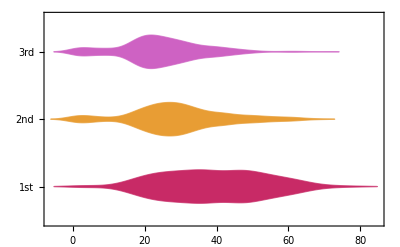
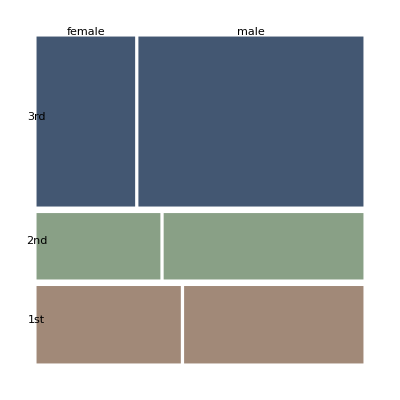
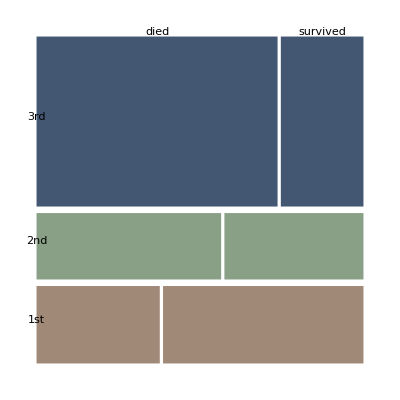
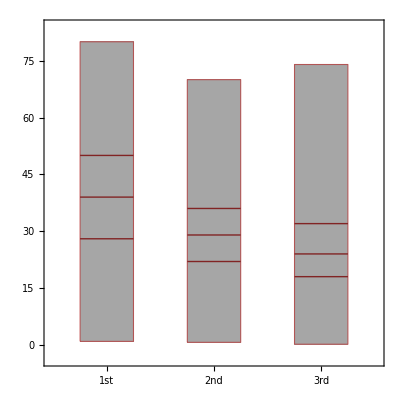
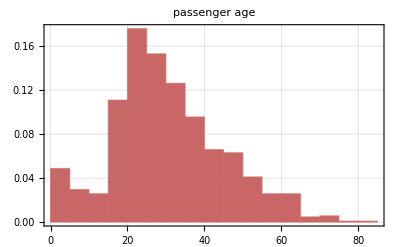
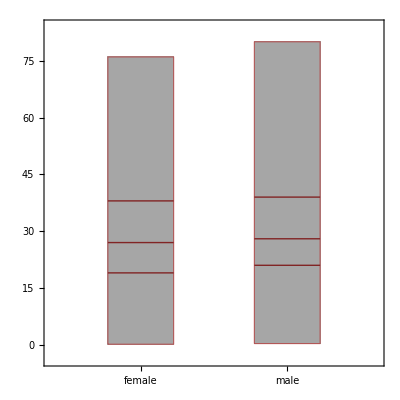
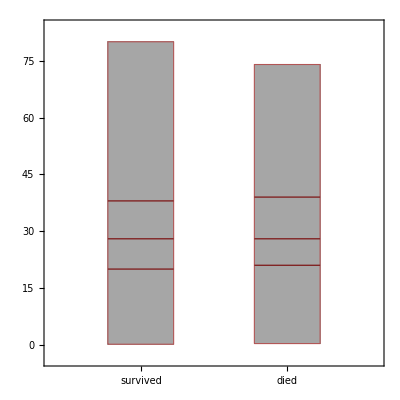
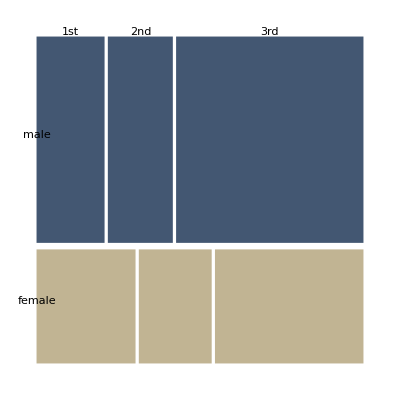
passenger class | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | passenger sex | -Graphics-
-Graphics- | -Graphics- | -Graphics- | passenger survival

```mathematica
Magnify[#, 1.] &@VariableDependenceGrid[titanicData, columnNames]
```

```mathematica
data = ExampleData[{"MachineLearning", "Titanic"}, "TrainingData"];
data = ((Flatten@*List) @@@ data)[[All, {1, 2, 3, -1}]];
trainingData = DeleteCases[data, {___, _Missing, ___}];
Dimensions[trainingData]
```

{732,4}

```mathematica
data = ExampleData[{"MachineLearning", "Titanic"}, "TestData"];
data = ((Flatten@*List) @@@ data)[[All, {1, 2, 3, -1}]];
testData = DeleteCases[data, {___, _Missing, ___}];
Dimensions[testData]
```

{314,4}

```mathematica
trainingData = trainingData /. {"survived" -> 1, "died" -> 0, "1st" -> 0, "2nd" -> 1, "3rd" -> 2, "male" -> 0, "female" -> 1};

testData = testData /. {"survived" -> 1, "died" -> 0, "1st" -> 1, "2nd" -> 2, "3rd" -> 3, "male" -> 0, "female" -> 1};
```

```mathematica
lfm = LinearModelFit[{trainingData[[All, 1 ;; -2]], trainingData[[All, -1]]}]
```

FittedModel[-0.0136025 #1+0.00515243 #2+0.634046 #3]

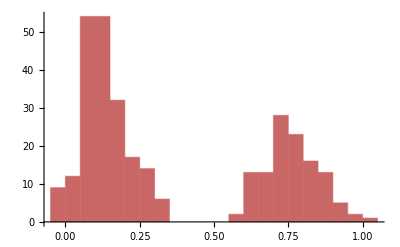

```mathematica
modelValues = lfm @@@ testData[[All, 1 ;; -2]];

Histogram[modelValues, 20]
```

```mathematica
testData[[1]]
```

{1,25.,1,0}

```mathematica
testLabels = testData[[All, -1]];
thRange = Range[0.1, 0.9, 0.025];
aROCs = Table[ToROCAssociation[{0, 1}, testLabels, 
	Map[If[# > θ, 1, 0] &, modelValues]], {θ, thRange}];
```

```mathematica
Through[ROCFunctions[{"PPV", "NPV", "TPR", "ACC", "SPC"}][aROCs[[3]]]]
```

{34/43,19/37,17/32,197/314,95/122}

```mathematica
ROCPlot[thRange, aROCs, 
	"PlotJoined" -> Automatic, 
	"ROCPointCallouts" -> True, 
	"ROCPointTooltips" -> True, 
	GridLines -> Automatic]
```

-Graphics-

```mathematica
thRange
```

{0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9}

```mathematica
FullForm[aROCs[[1]]]
```

Association[Rule["TruePositive",61],Rule["FalsePositive",14],Rule["TrueNegative",108],Rule["FalseNegative",131]]

## Conclusion

The quite revolution of numerical prediction has brought

The quiet revolution of numerical weather models has been boosting a consistent increase in accuracy and extension of weather predictions. The progress require keeping clarifying the boundary between weather and climate.  
Extratropical cyclones, storm tracks.

there is never a sharp distincion

# Prediction Opportunity

BX Pan
2017.10.24

## Prediction Opportunity

On the Long Term Prediction of Chaotic System

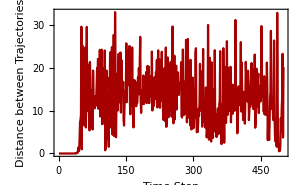
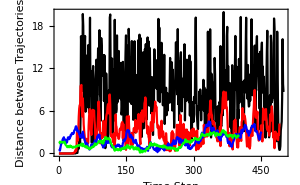
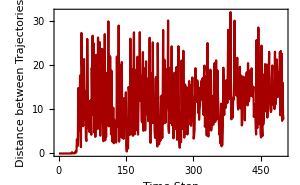
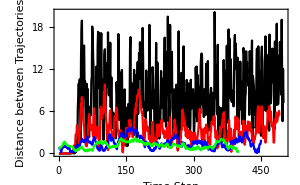
| Trajectory_1 | Trajectory_2 | L2 Distance | L2 Distance of Temporal Mean
{0, 1, 1} | -Graphics3D- | -Graphics3D- | -Graphics- | -Graphics-
{-10, 10, 10} | -Graphics3D- | -Graphics3D- | -Graphics- | -Graphics-Lorenz System Simulations by Pertubating y_0 of 1/10000000000

```mathematica
scale=ImageResize[ImageCrop[-Graphics-],800];
Labeled[scale,"Time series depicting variations of weather/climate, 
Next Generation Earth System Prediction: Strategies for Subseasonal to Seasonal Forecasts. Washington, DC: The National Academies Press. doi: 10.17226/21873.",Bottom]
```

-Graphics-Time series depicting variations of weather/climate, 
Next Generation Earth System Prediction: Strategies for Subseasonal to Seasonal Forecasts. Washington, DC: The National Academies Press. doi: 10.17226/21873.

Climate system undergoes different scenarios through its evolution. The slowly varying components can provide information for extended forecast. When dynamical models are initialized at certain phase of these  phenomena, the model forecasts match observations with more fidelity than the neutral phases. These intervals are named as forecast windows and believed to bring prediction opportunities.

## Examples

ENSO

```mathematica
impactLaNina=ImageCrop[-Graphics-];
impactElNino=ImageCrop[-Graphics-];
enso=ImageCrop[-Graphics-];
GraphicsRow[{ImageResize[enso,500],ImageResize[impactLaNina,500],ImageResize[impactElNino,500]},ImageSize->Full]
```

-Graphics-

MJO

```mathematica
mjo=ImageCrop[-Graphics-];
ImageResize[mjo,1000]
```

-Graphics-

-Graphics- | -Graphics-"Meet the MJO, By Jon Gottschalck, NOAA Climate Prediction Center with Andrea Ray, WWA

Stratospheric Sudden Warming

When initialized at the onset date of stratospheric sudden warmings, the model forecasts faithfully reproduce the observed mean tropospheric conditions in the months following the stratospheric sudden warmings. Compared with an equivalent set of forecasts that are not initialized during stratospheric sudden warmings, we document enhanced forecast skill for atmospheric circulation patterns, surface temperatures over northern Russia and eastern Canada and North Atlantic precipitation. We suggest that seasonal forecast systems initialized during stratospheric sudden warmings are likely to yield significantly greater forecast skill in some regions.
e identified
the stratosphere as an untapped source of enhanced seasonal
predictability.

Seasonal forecast systems based on dynamical models are able to
capture the average tropospheric state following SSWs to some
extent12, but it is not evident that this is associated with a detectable
increase in forecast skill of surface weather13. Here we demonstrate
that a dynamical forecast system initialized at the time of a SSW
is able to predict the mean tropospheric circulation response in
the following months

The dynamical forecast system in this study employs the Canadian
Middle Atmosphere Model14. Retrospective forecasts (also
known as hindcasts) are initialized at 20 SSW dates between
1970 and 2009 (hereafter referred to as the SSW forecasts), each
consisting of 10 ensemble members.

Methodology

Cluster prediction results according to climate conditions and compare with long-run/neutral conditions

## Seeking Forecast windows ⟶ MJO

Parameterization of MJO

1, filter OLR to retain only frequencies associated with the MJO. 
2, Filtered OLR between 208S and 208N is then subjected to a standard covariance matrix EOF analysis that retains the local variance of the OLR fluctuations.

```mathematica
MJO=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/MJO/OMI","Table"];
```

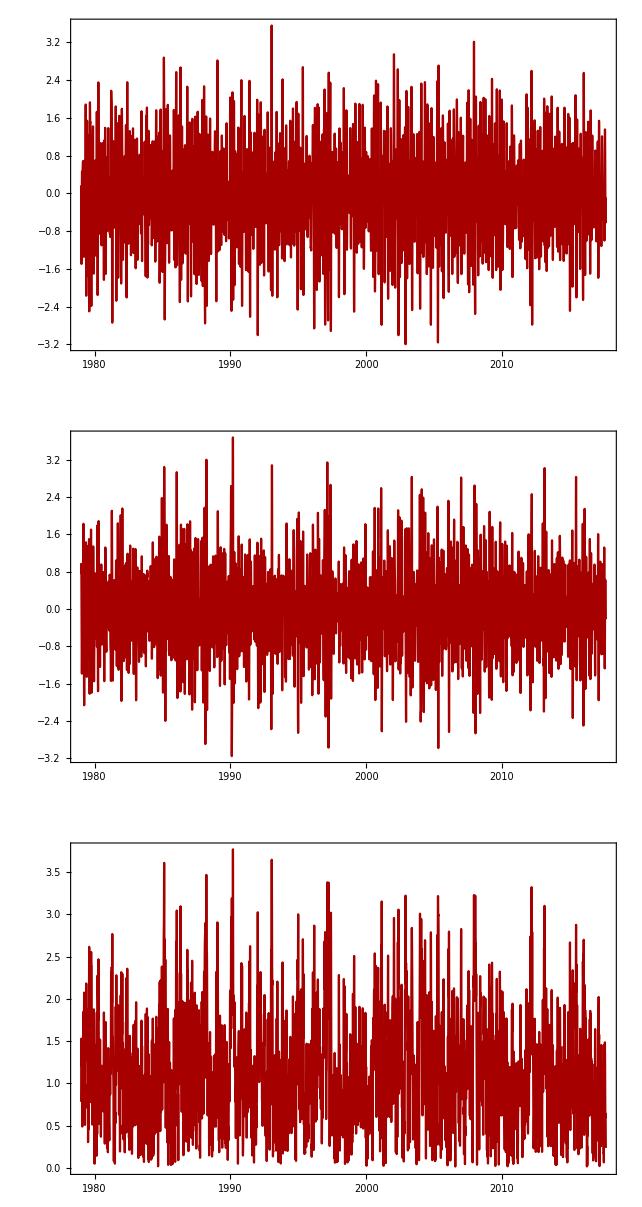

```mathematica
GraphicsColumn[{DateListPlot[TimeSeries[MJO[[;;,5]],{{1979,1,1}}],ImageSize->600],
                DateListPlot[TimeSeries[MJO[[;;,6]],{{1979,1,1}}],ImageSize->600],
                DateListPlot[TimeSeries[MJO[[;;,7]],{{1979,1,1}}],ImageSize->600]}]
```

## Seeking Forecast windows ⟶ ENSO